# Projection Methods for A x=b for A∈ℝ^(n×n) Notation from Saad

The original problem size n is too big.  The plan is to reduce the dimension by looking for an approximate solution x̂ based on an m dimensional subspace 
	𝒦_m⊂ℝ^n
by enforcing m conditions on the residual
	A x̂-b
designed to make the residual small.  Since it is no longer the “big” problem we will need to iterate and we “hope” that the iteration converges. In the real world we want some assurance that: The iteration converges and some quantitative information about how fast it should converge.  We will have an initial condition x_0 that we seek to improve to 
	x̂=x_0+δ where δ∈𝒦.
A projection method is defined by the search space 𝒦 and requiring the residual A x̂-b to be orthogonal to a (possibly different subspace) ℒ. In other words we want to find δ∈𝒦 satisfying
	(A (x_0+δ)-b)⊥ℒ
For this to make sense we need dim(𝒦)=dim(ℒ).  If 𝒦=ℒ this is an orthogonal projection method. If 𝒦≠ℒ this is an oblique projection method.

## Skeleton Algorithm 5.1

To implement this we choose basis
	V=[v_1|…|v_m] and W=[w_1|…|w_m] 
so that  𝒦=span(V) and ℒ=span(W) to get the representation x̂=x_0+V y with y∈ℝ^m when you plug in the orhtogonality condition is
	Wᵀ.A .V.y+Wᵀ.A .x_0-Wᵀ.b=0  or equivalently Wᵀ.A.V.y=Wᵀ.(b-A.x_0).
All we need to do is solve this small m×m linear system for y and build our new (and hopefully)
improved  iterate
	x_1=x_0+V y=x_0+V.(Wᵀ.A.V)^-1.(b-A.x_0)
and then repeat as needed see Algorithm 5.1

## Theory and Interpretation

P5.2 If A is SPD and 𝒦=ℒ and x_*=A^-1 b then 
	x_1=argmin_(x∈x_0+𝒦) A.(x-x_*).(x-x_*)=argmin_(x∈x_0+𝒦) √(A.(x-x_*).(x-x_*))

P5.3 If ℒ=A .𝒦 then 
	x_1=argmin_(x∈x_0+𝒦) ||A.x-b||

P5.4 If ℒ=A .𝒦 and  
	x_1=argmin_(x∈x_0+𝒦) ||A.x-b||
then 
	b-A.x_1=(I-P).(b-A.x_0) 
where P is the projection onto ℒ=A.𝒦

P5 .5 If A is SPD and 𝒦=ℒ and x_*=A^-1 b then
	x_*-x_1=(I-P).(x_*-x_0)
where P is the orthogonal projector onto 𝒦 with respect to the A inner product
	<x,y>_A=(A.x).y=x.(A.y)=<S.x,S.y>
where S=√A.

P5 .6 If A.𝒦=𝒦=ℒ and b∈𝒦 then
	x_1=A^-1.b

## Simple 1D Subspace Algorithms

We need to do multiple steps and pick smart spaces 𝒦_k and ℒ_k to define the iteration from our approximation x_k to x_(k+1).  Our first attempts will use one dimensional spaces 𝒦=span(v) and ℒ=span(w) and all we need to do is find the value of α in
	x_0+α v  
which satisfies the inner product equation below
	⟨w,A.(x_0+α v)-b⟩=0.
Solving gives the update value
	α=⟨A.(b-A.x_0), w⟩/⟨A.v, w⟩=⟨A.r_0, w⟩/⟨A.v, w⟩ 
To avoid indexing and indicate that in practice you overwrite variables the book starts using arrows  “⟵” to denote updates

### Steepest Descent

An SPD matrix A defines a natural cost function f(x)=1/2 x.A.x-b.x which has the negative of the residual -r=A.x-b as its gradient. The orthogonal projection algorithm searching in the downhill direction i.e. 𝒦=ℒ=span{r} defines the Steepest Descent algorithm.    In the natural arrow form we have
	r | ⟵ | b-A.x
α | ⟵ | (r.r)/(r.A.r)
x | ⟵ | x+α r
which can be rearranged to need only one matrix-vector multiplication.

Steepest Descent (inner loop)
	p | ⟵ | A.r
α | ⟵ | (r.r)/(p.r)
x | ⟵ | x+α r
r | ⟵ | r-α p
This inner loop updates x and r at the cost of one matrix-vector multiply and a bunch of less intensive arithmetic.

To turn this into an algorithm we need to put it inside a loop which terminates when ||r|| is sufficiently small. For right now I a just going to run it a fixed number of times on a randomly generated test problem and look at the results.

```mathematica
SDStep[A_][{x_,r_}]:= Module[{p=A.r,α,xOut,rOut},
α=r.r/(p.r);
xOut =x+α r;
rOut= r- α p;
{xOut,rOut}
]

n=12;
A=RandomReal[{-1,1},{n,n}];A=A.Aᵀ; b=RandomReal[{-1,1},n];
λs=Eigenvalues[A];
Five14Ratio=(λs⟦1⟧-λs⟦-1⟧)/(λs⟦1⟧+λs⟦-1⟧);

xStar=LinearSolve[A,b]; MaxIter=100;
x0=ConstantArray[0,n]; r=b;
xrData=NestList[SDStep[A],{x0,r},MaxIter];
TabView[{
"x"->MatrixPlot[xrData⟦All,1⟧,PlotLegends->Automatic,AspectRatio->1],
"r"->MatrixPlot[xrData⟦All,2⟧,PlotLegends->Automatic,AspectRatio->1],
"||r||"->ListLogPlot[Map[Norm,xrData⟦All,2⟧],PlotLegends->Automatic,Joined->True],
"||x-x_*||"->ListLogPlot[{Map[Norm[#-xStar]&,xrData⟦All,1⟧],Norm[xStar] Five14Ratio^Range[MaxIter]},PlotLegends->Automatic,Joined->True,PlotLabel->Five14Ratio]
}]
```

1234

This is not the greatest algorithm in the world!

### 1D Minimum Residual

Taking 𝒱=span(r) and ℒ=span(w)=span(A.r)-A.𝒱.  This algorithm minimizes the residual over the search space. The natural iteration is
	r | ⟵ | b-A.x
α | ⟵ | (A.r.r)/((A.r).(A.r))
x | ⟵ | x+α r
Rearranging gives us a version that uses only one matrix-vector product.

1D Min Residual (inner loop)
	α | ⟵ | (p.r)/(p.p)
x | ⟵ | x+α r
r | ⟵ | r-α p
p | ⟵ | A.r
This inner loop updates x and rand  at the cost of one matrix-vector multiply and a bunch of less intensive arithmetic.

To turn this into an algorithm we need to put it inside a loop which terminates when ||r|| is sufficiently small. For right now I am just going to run it a fixed number of times on a randomly generated test problem and look at the results.  If A+Aᵀ is SPD then α is positive and the algorithm heads down hill!

```mathematica
MRStep[A_][{x_,r_,p_}]:= Module[{α,xOut,rOut,pOut},
α=p.r/(p.p);
xOut =x+α r;
rOut= r- α p;
pOut=A.rOut;
{xOut,rOut,pOut}
]

Clear[μ]
n=12; ϵ=0.1;
A=RandomReal[{-1,1},{n,n}]; b=RandomReal[{-1,1},n];
(* Defining the function below 5.20 *)
μ[B_]:= Eigenvalues[B+Bᵀ,-1]⟦1⟧/2
(* Making sure A+Aᵀ is SPD *)
λMin=μ[A];
Eigenvalues[A]
If[λMin<ϵ,A=A+(ϵ/2-λMin) IdentityMatrix[n]];
λs=Eigenvalues[A+Aᵀ]
```

{-0.376791+1.90417 ⅈ,-0.376791-1.90417 ⅈ,-1.49937+0.304156 ⅈ,-1.49937-0.304156 ⅈ,1.5112+0. ⅈ,-0.0438236+1.32734 ⅈ,-0.0438236-1.32734 ⅈ,1.15912+0.242669 ⅈ,1.15912-0.242669 ⅈ,-0.806172+0.156624 ⅈ,-0.806172-0.156624 ⅈ,-0.232262+0. ⅈ}

{-4.94686,4.14755,3.4181,-3.20531,3.07505,-2.46014,-1.81573,1.73239,-1.41464,0.468356,-0.423807,0.1}

```mathematica
λMin=λs⟦-1⟧;σ=Norm[A];μX=λMin/2;
Five15Ratio=(1-μX^2/σ^2)^0.5
Five20Ratio=(1-μ[A]/μ[Inverse[A]])^0.5
xStar=LinearSolve[A,b]; MaxIter=20;
x0=ConstantArray[0,n]; r=b;p=A.r;
xrpData=NestList[MRStep[A],{x0,r,p},MaxIter];
ListLogPlot[Hmm={Map[Norm,xrpData⟦All,2⟧],Norm[r] Five15Ratio^Range[MaxIter],Norm[r] Five20Ratio^Range[MaxIter]},PlotLegends->{"||r_k||=||A.x_k-b||","5.15","5.20"},Joined->True]
```

0.999902

4.69973×10^-17+0.767524 ⅈ

```mathematica
Hmm
```

{{1.97891,1.91739,1.9123,1.91207,1.91206,1.91206,1.91206,1.91206,1.91206,1.91206,1.91206,1.91206,1.91206,1.91206,1.91206,1.91206,1.91206,1.91206,1.91206,1.91206,1.91206},{1.97871,1.97852,1.97833,1.97813,1.97794,1.97774,1.97755,1.97735,1.97716,1.97697,1.97677,1.97658,1.97638,1.97619,1.976,1.9758,1.97561,1.97541,1.97522,1.97503},{9.30033×10^-17+1.51886 ⅈ,-1.16576+1.42765×10^-16 ⅈ,-1.64363×10^-16-0.894749 ⅈ,0.686741-1.68203×10^-16 ⅈ,1.61375×10^-16+0.52709 ⅈ,-0.404554+1.48631×10^-16 ⅈ,-1.33091×10^-16-0.310505 ⅈ,0.23832-1.16743×10^-16 ⅈ,1.00803×10^-16+0.182916 ⅈ,-0.140392+8.59656×10^-17 ⅈ,-7.25787×10^-17-0.107755 ⅈ,0.0827042-6.077×10^-17 ⅈ,5.05293×10^-17+0.0634774 ⅈ,-0.0487204+4.17657×10^-17 ⅈ,-3.43459×10^-17-0.0373941 ⅈ,0.0287008-2.81187×10^-17 ⅈ,2.29306×10^-17+0.0220286 ⅈ,-0.0169075+1.86351×10^-17 ⅈ,-1.50975×10^-17-0.0129769 ⅈ,0.00996006-1.21975×10^-17 ⅈ}}

0.999902

4.69973×10^-17+0.767524 ⅈ

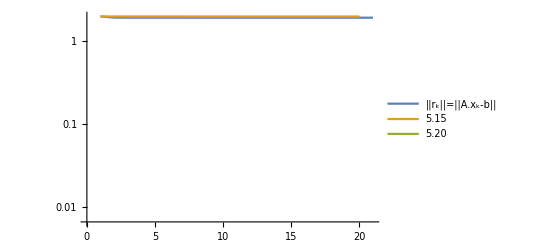

1234

```mathematica
TabView[{
"x"->MatrixPlot[xrpData⟦All,1⟧,PlotLegends->Automatic,AspectRatio->1],
"r"->MatrixPlot[xrpData⟦All,2⟧,PlotLegends->Automatic,AspectRatio->1],
"||r||"->ListLogPlot[{Map[Norm,xrpData⟦All,2⟧],Norm[r] Five15Ratio^Range[MaxIter],Norm[r] Five20Ratio^Range[MaxIter]},PlotLegends->{"||r_k||=||A.x_k-b||","5.15","5.20"},Joined->True],
"||x-x_*||"->ListLogPlot[{Map[Norm[#-xStar]&,xrpData⟦All,1⟧],Norm[x0-xStar] Five15Ratio^Range[MaxIter],Norm[x0-xStar] Five20Ratio^Range[MaxIter]},
PlotLegends->{"||x_k-x_*||","Thm 5.15","Thm 5.20"},Joined->True,PlotLabel->"5.15 & 5.20"]
}]
```

```mathematica
μ[A]
```

0.05[{{-0.582616,-0.545908,0.311144,0.170444,0.224693,0.544965,-0.0555246,0.813733,0.0961529,0.711676,0.810296,-0.641569},{0.839195,-0.341882,-0.17504,0.920321,0.617144,-0.460752,0.035529,0.249423,-0.831371,-0.731592,0.933037,-0.290122},{0.981555,0.609776,-0.0447117,0.244256,-0.743775,-0.0402782,-0.414374,0.591956,-0.663588,0.464846,-0.636031,0.607215},{0.806742,-0.929533,-0.80299,-0.754952,0.0891935,-0.396397,0.95188,0.6561,0.693546,-0.785245,-0.743372,0.811641},{-0.442759,0.663638,-0.0802543,-0.149448,-0.0971151,-0.735856,0.406559,-0.841097,0.953201,0.987596,-0.0549263,0.108992},{0.0385258,0.488072,-0.612807,-0.234157,0.313518,-0.851459,-0.114957,0.962767,0.97835,-0.521918,0.879422,-0.578591},{0.0199161,0.747595,-0.912061,0.164724,0.2792,-0.0730589,0.966151,-0.677885,-0.898852,-0.0524353,-0.943394,0.241364},{-0.920427,-0.693269,-0.921996,0.79535,-0.641323,-0.0295392,0.61832,0.482359,0.431268,0.0151049,0.17027,-0.708171},{-0.953317,-0.0299199,0.594467,-0.881191,-0.704799,0.0903732,0.340787,0.505162,0.491146,-0.404833,-0.238964,-0.277489},{-0.648905,0.123749,0.613261,-0.858346,0.615566,0.0291647,0.108837,-0.361437,-0.359786,0.893864,0.21689,0.230567},{0.0391193,-0.100158,0.134071,0.150214,-0.503106,0.0757853,0.387079,-0.20095,-0.424569,0.776734,-0.420961,-0.978016},{-0.80912,-0.262586,-0.682848,0.118337,0.253932,-0.129541,0.632498,0.0108905,0.347419,-0.124056,-0.296898,0.132274}}]

This algorithm is doing a lot better than the 5.10!